```mathematica
(*Mathematica*)
```

```mathematica
(*2nd minimal Pisot extended :(z^4-z^3-1)*(z^2+z+1)*)
p[x_]=ExpandAll[-1-x-x^2-x^3+x^6]
```

-1-x-x^2-x^3+x^6

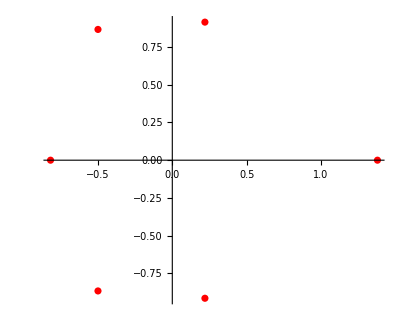

```mathematica
ComplexListPlot[z/.NSolve[p[z]==0,z],PlotStyle->Red]
```

```mathematica
ϕ=N[GoldenRatio];
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
sc=2.0;
```

```mathematica
f[z_]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)*(z^2-(sc*r[6])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1)*(-(sc*r[6]*z)^2+1))
```

-((0.737369+0.67549 ⅈ) z^12 (-7.62066+z^2) (-2.68417+z^2) ((2.-3.4641 ⅈ)+z^2) ((2.+3.4641 ⅈ)+z^2) ((3.15242-1.60543 ⅈ)+z^2) ((3.15242+1.60543 ⅈ)+z^2))/((1-7.62066 z^2) (1-2.68417 z^2) (1+(2.-3.4641 ⅈ) z^2) (1+(2.+3.4641 ⅈ) z^2) (1+(3.15242-1.60543 ⅈ) z^2) (1+(3.15242+1.60543 ⅈ) z^2))

```mathematica
g0=JuliaSetPlot[f[z],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All];
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by Roger Lee .10Bagula 18 July 2023 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nn=4,nzold=0},
	For[
		escapeCount = 0,
		(Abs[nz]<64) && (escapeCount < 2048) &&(Abs[nz-nzold]>0.5*10^(-3)),
		nzold=nz;
		nz=f[nz];
		++escapeCount
	];
	
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),escapeCount*(2*Pi-Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]]),escapeCount*(2*Pi-Arg[nz]*(Max[1-Arg[nz]/(2*Pi),Arg[nz]/(2*Pi)]))]
	
	
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.75001,2.75,1000},{-2.5001,2.75,1000}}];
```

General::munfl: (-1.44449×10^-27+1.1143×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.80776×10^-33+2.31117×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.73857×10^-34-2.96469×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.8157×10^-29-7.63417×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.10244×10^-31+5.80565×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.29883×10^-27+8.09755×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.53179×10^-27-2.17268×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.92435×10^-33-1.14781×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.73242×10^-27+1.52038×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.46703×10^-30+2.28665×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.92747×10^-34-1.67755×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.75968×10^-37+4.08833×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.47497×10^-33+1.65854×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.08172×10^-30+1.10488×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.23249×10^-29+1.97209×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.12474×10^-32+2.40602×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.15535×10^-35+1.8376×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.03782×10^-26+1.15879×10^-26 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (5.55487×10^-30-2.68756×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.20867×10^-36-1.44391×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.19899×10^-27+8.64853×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-2.54573×10^-30-5.1718×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.94934×10^-31-5.42369×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.97253×10^-34+4.70637×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.74478×10^-28+1.47692×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.12831×10^-27+3.00746×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.81471×10^-35+1.87932×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-5.30649×10^-31-3.95081×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.6129×10^-30-7.38753×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.30085×10^-27+1.59632×10^-26 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.47131×10^-30+3.98029×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.63781×10^-35-5.2426×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.15862×10^-35-1.55436×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.86684×10^-35+3.42678×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.01475×10^-36-3.78537×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.29123×10^-30+1.1692×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.30504×10^-32-8.88445×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.73037×10^-29+1.13367×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.95746×10^-33-2.1988×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-4.80837×10^-34+2.77452×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.57663×10^-29+1.99952×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.56922×10^-32-1.70835×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-4.02296×10^-33-1.41447×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.6019×10^-27+3.39986×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.92346×10^-32+5.10727×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-3.26959×10^-32-4.62809×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.29891×10^-36-1.10261×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.86474×10^-34+1.35192×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.5944×10^-36+1.77947×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.38332×10^-26-8.87702×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.2165×10^-27-1.41793×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-5.12274×10^-30-2.15701×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.32109×10^-34+5.88751×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.20338×10^-29-1.2197×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-8.64061×10^-33-7.38713×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.17459×10^-28+5.01879×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.0658×10^-26+9.04768×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.33818×10^-29+1.68585×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.737369-0.67549 ⅈ) (-9.9344×10^-307+9.19165×10^-307 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.1562×10^-34+3.9516×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-3.07854×10^-29-1.03783×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.72547×10^-34+2.56492×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.03404×10^-28+2.73137×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.19987×10^-31+8.92439×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.85805×10^-27+1.04569×10^-26 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.47967×10^-27-2.19259×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.0462×10^-34-7.41546×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.43342×10^-31+2.95276×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.82861×10^-28+1.27879×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.633×10^-26-3.42304×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.37517×10^-36+1.13558×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.58346×10^-30-7.31498×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
g1=ListPlot3D[N[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=ListDensityPlot[arraym,   Mesh -> False,     AspectRatio -> Automatic, ColorFunction->(Hue[(2*#)]&),ImageSize->2000,Axes->False,ImageSize->2000,Frame->False];
```

```mathematica
colortab=Reverse[Union[Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/6,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/12]]]];
```

```mathematica
Length[%]
```

447

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/447,1,Ceiling[447*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=Rasterize[ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["j_1000_2ndMinimal_Pisot_extended_z12_Herman_rings_3d_Inside_Outside_monitor_grid.jpg",GraphicsGrid[{{g0,g1},{g2,g3}},ImageSize->{{4000,4000}}]]
```

j_1000_2ndMinimal_Pisot_extended_z12_Herman_rings_3d_Inside_Outside_monitor_grid.jpg

```mathematica
(*end*)
```